```mathematica
NS["diff_statistics","C:\\Users\\pglpm\\repositories\\neurobayes"]
```

```mathematica
cc[s_,nn_,m_]=Binomial[s*nn,m]/Binomial[nn,m]
```

Binomial[nn s,m]/Binomial[nn,m]

```mathematica
gg[s_,ss_,n_,nn_]=Binomial[n,n*s]*Binomial[nn-n,nn*ss-n*s]/Binomial[nn,nn*ss]
```

(Binomial[n,n s] Binomial[-n+nn,-n s+nn ss])/Binomial[nn,nn ss]

```mathematica
nn=40;n=4;m=2;
st0=(cc[#,nn,m]&)/@(Range[0,nn]/nn);
st1=(cc[#,n,m]&)/@(Range[0,n]/n);
ggt=Table[gg[s,ss,n,nn],{s,Range[0,n]/n},{ss,Range[0,nn]/nn}];
st1b=st1.ggt;
```

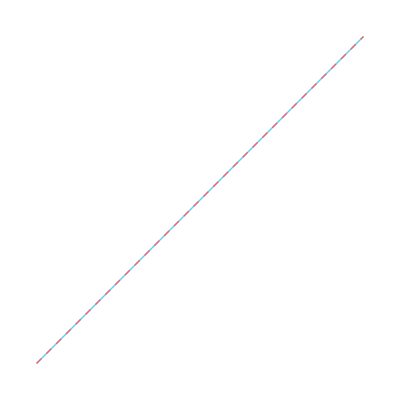

```mathematica
ListPlot[{T@{st0,st1b},T@{st0,st0}},AspectRatio->1,Joined->True]
```